```mathematica
Clear["Global`*"];
```

```mathematica
<</home/xierr/.Mathematica/Applications/CustomTicks/CustomTicks.m
```

```mathematica
tlen=0.014;tickd=In;thick=Thickness[0.002];ip={{80,30},{60,30}};
```

```mathematica
cliprange[points_List,xmax_:3.99]:=Module[{xmaxpos},xmaxpos=Position[points,Nearest[points[[All,1]],xmax][[1]]][[1,1]];
points[[1;;xmaxpos]]];
```

```mathematica
B[β_?NumericQ]=(Gamma[(β+2)/2]/Gamma[(β+1)/2])^2;
A[β_?NumericQ]=2/Gamma[(β+1)/2] B[β]^((β+1)/2);
p[s_?NumericQ,β_?NumericQ]:=A[β] s^β ⅇ^(-B[β] s^2)
```

```mathematica
nnd1=cliprange[Import["AFilha_NND.txt","Table"]];
nnd4=cliprange[Import["Grande_NND.txt","Table"]];
nnd2=cliprange[Import["OPrimo_NND.txt","Table"]];
nnd3=cliprange[Import["OsMaias_NND.txt","Table"]];
```

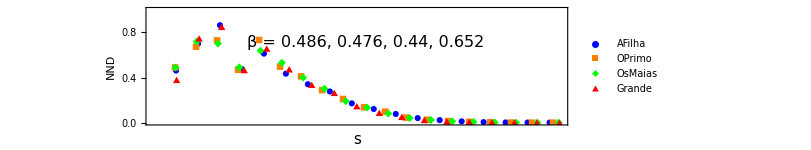

```mathematica
nndpoints=ListPlot[{nnd1,nnd2,nnd3,nnd4}(*use your data*),PlotRange->{{0,4},{0,1}},AspectRatio->1/4.(*specify the height-to-width ratio*),ImageSize->600,PlotMarkers->Automatic,Frame->True,PlotStyle->{Blue, Orange, Green, Red},
(*********************Frame Ticks***********************)
ImagePadding->ip,PlotRangeClipping->False,FrameStyle->Directive[thick,Black,FontSize->20,FontFamily->"Times New Roman"],FrameTicksStyle->Directive[thick,"Label", 15],FrameTicks->{{LinTicks[{0,0.2,0.4,0.6,0.8},{0.1,0.3,0.5,0.7,0.9},MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->True,TickDirection->tickd],(*left*)
LinTicks[{0,0.2,0.4,0.6,0.8},{0.1,0.3,0.5,0.7,0.9},MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->False,TickDirection->tickd,ShowTickLabels->False]},(*right*){LinTicks[{0,1,2,3,4},{0.5,1.5,2.5,3.5},MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->False],(*down*)
LinTicks[{0,1,2,3,4},{0.5,1.5,2.5,3.5},MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->True]}},(*up*)FrameLabel->{None,Style["NND",FontFamily->"Times New Roman",15]},
(***************************************)PlotLegends->Placed[PointLegend[Automatic,Style[#,10,FontFamily->"Times New Roman"]&/@{"AFilha","OPrimo","OsMaias","Grande"},LegendFunction->Framed,LegendMargins->0],{(*legend position*)Scaled[0.85],Scaled[0.5]}],Epilog->{Text[Style["  β = 0.486, 0.476, 0.44, 0.652",FontSize->16,FontFamily->"Times New Roman"],Scaled[{0.52,0.7}]],Text[Style["StyleBox[\"s\",FontSlant->\"Italic\"]",FontSize->15,FontFamily->"Times New Roman"],Scaled[{0.5,-0.12}]]}]
```

```mathematica
nlm1=NonlinearModelFit[nnd1,p[s,β],β,s]
```

FittedModel[p[s,0.486386]]

```mathematica
clippoints = Table[{s,Normal[nlm1]},{s,0.0001,4,0.04}] ;
```

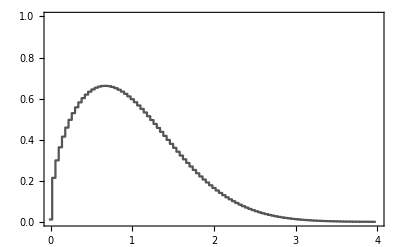

```mathematica
nndmat=ListStepPlot[clippoints,Center,AxesOrigin->{0,0},PlotRange->{{0,4},{0,1}},PlotStyle->Lighter[Black],Frame->True]
```

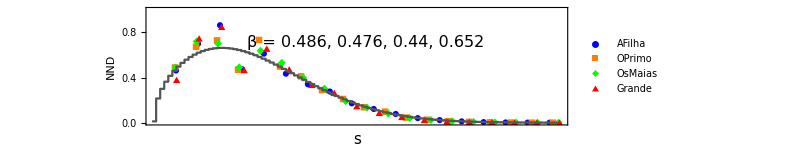

```mathematica
p1=Show[nndpoints,nndmat]
```

```mathematica
logpoints=clippoints/.{x_,y_}:>{x,Log10[y]};
logran=MinMax[logpoints[[All,2]]]
logrange=logran+{-0.1,0.4}
```

{-3.38095,-0.178995}

{-3.48095,0.221005}

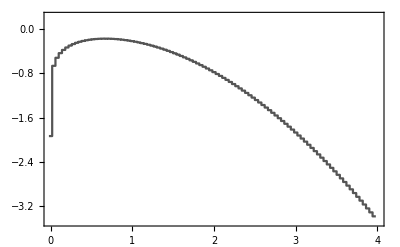

```mathematica
nndmatlog=ListStepPlot[logpoints,Center,AxesOrigin->{0,0},PlotRange->{{0,4},logrange},PlotStyle->Lighter[Black],Frame->True]
```

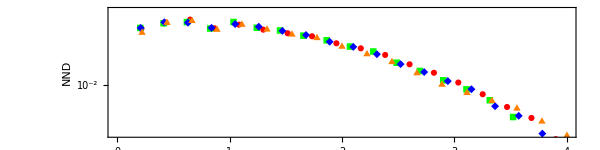

```mathematica
lognndpoints=ListPlot[{nnd1,nnd2,nnd3,nnd4}/.{x_,y_}:>{x,Log10[y]},PlotRange->{{0,4},logrange},AspectRatio->1/4.,ImageSize->600,PlotMarkers->Automatic,Frame->True,PlotStyle->{Red, Green, Blue, Orange},
(*********************Frame Ticks***********************)
ImagePadding->ip,FrameStyle->Directive[thick,Black,FontSize->20,FontFamily->"Times New Roman"],FrameTicksStyle->Directive[thick,"Label", 15],FrameTicks->{{LogTicks[-12,0,TickLabelStep->1,MajorTickLength->2tlen,MinorTickLength->0.7tlen,ShowFirst->True,ShowLast->True,TickDirection->tickd,ShowTickLabels->True]/.{DisplayForm[SuperscriptBox[10,0]]->"1"},
LogTicks[-12,0,TickLabelStep->1,MajorTickLength->2tlen,MinorTickLength->0.7tlen,TickDirection->tickd,ShowTickLabels->False]},{LinTicks[{0,1,2,3,4},{0.5,1.5,2.5,3.5},MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->True],
LinTicks[{0,1,2,3,4},{0.5,1.5,2.5,3.5},MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->False]}},FrameLabel->{None,Style["NND",FontFamily->"Times New Roman",15]}]
```

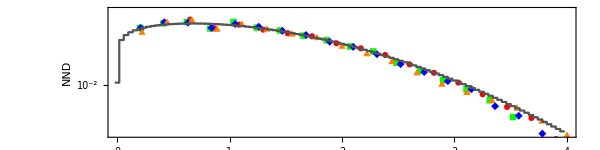

```mathematica
p2=Show[lognndpoints,nndmatlog]
```

```mathematica
ξsb[ξb_?NumericQ]:=Gamma[ξb+1/2]/Gamma[ξb];
NV[L_?NumericQ,ξb_?NumericQ, f_?NumericQ]:= (1-f)L+((ξsb[ξb]/(√ξb))^-2-1) (L/f)^2;
```

```mathematica
nv1=Import["AFilha_variance.txt","Table"];
nv4=Import["Grande_variance.txt","Table"];
nv2=Import["OPrimo_variance.txt","Table"];
nv3=Import["OsMaias_variance.txt","Table"];
```

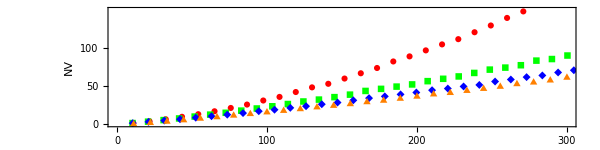

```mathematica
nvpoints=ListPlot[{nv1,nv2,nv3,nv4}(*use your data*),PlotRange->{{0,300},{0,150}},DataRange->{{0,300},{0,150}},AspectRatio->1/4.(*specify the height-to-width ratio*),ImageSize->600,PlotMarkers->Automatic,Frame->True,PlotStyle->{Red, Green, Blue, Orange},
(*********************Frame Ticks***********************)
ImagePadding->ip,FrameStyle->Directive[thick,Black,FontSize->20,FontFamily->"Times New Roman"],FrameTicksStyle->Directive[thick,"Label", 15],FrameTicks->{{LinTicks[Range[0,150,50],Range[25,125,50],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->True,ShowLast->False,TickDirection->tickd],(*left*)
LinTicks[Range[0,150,50],Range[25,125,50],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->False,TickDirection->tickd,ShowTickLabels->False]},(*right*){LinTicks[Range[0,300,100],Range[50,250,100],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->True],(*down*)
LinTicks[Range[0,300,100],Range[50,250,100],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->False]}},(*up*)FrameLabel->{Style["StyleBox[\"L\",FontSlant->\"Italic\"]",FontSize->15,FontFamily->"Times New Roman"],Style["NV",FontFamily->"Times New Roman",15]}]
```

```mathematica
nlm1=NonlinearModelFit[nv1,NV[L,ξb,f],{ξb,f},L];
nlm2=NonlinearModelFit[nv2,NV[L,ξb,f],{ξb,f},L];
nlm3=NonlinearModelFit[nv3,NV[L,ξb,f],{ξb,f},L];
nlm4=NonlinearModelFit[nv4,NV[L,ξb,f],{ξb,f},L];
```

```mathematica
nlm1v1=NonlinearModelFit[nv1,NV[L,ξb,0.95],{ξb},L];
nlm2v1=NonlinearModelFit[nv2,NV[L,ξb,0.95],{ξb},L];
nlm3v1=NonlinearModelFit[nv3,NV[L,ξb,0.95],{ξb},L];
nlm4v1=NonlinearModelFit[nv4,NV[L,ξb,0.95],{ξb},L];
```

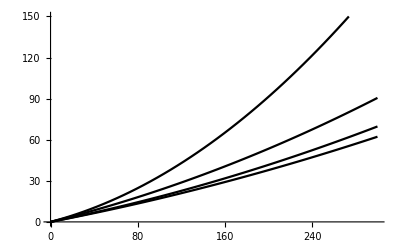

```mathematica
nvcurv=Plot[{Normal[nlm1],Normal[nlm2],Normal[nlm3],Normal[nlm4]},{L,0,300},PlotStyle->Black,PlotRange->{{0,300},{0,150}}]
```

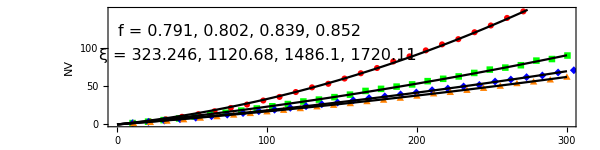

```mathematica
p3=Show[nvpoints,nvcurv,(*we want nvcurv as background*)Epilog->{Text[Style["StyleBox[\"f\",FontSlant->\"Italic\"] = 0.791, 0.802, 0.839, 0.852",FontSize->16,FontFamily->"Times New Roman"],Scaled[{0.28,0.8}]],Text[Style["ξ̄ = 323.246, 1120.68, 1486.1, 1720.11",FontSize->16,FontFamily->"Times New Roman"],Scaled[{0.32,0.6}]]}]
```

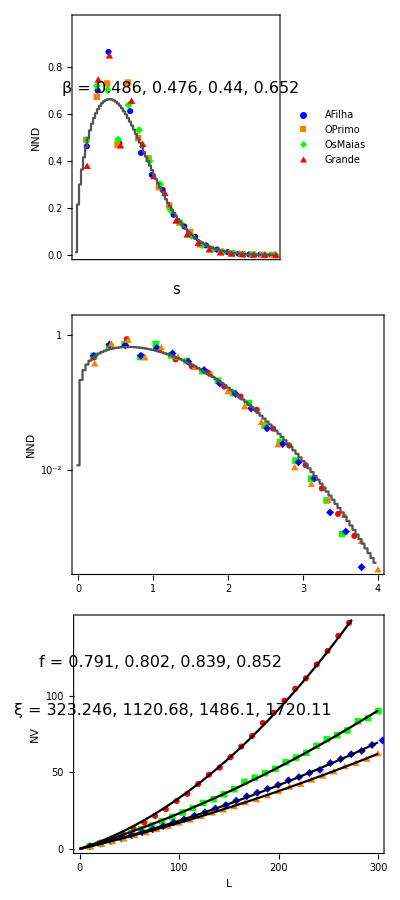

```mathematica
fig=Column[{p1,p2,p3},Spacings->-4.5]
```

```mathematica
Export["Portuguese.eps",fig]
```

Portuguese.eps